```mathematica
ClearAll["Global`*"]
```

```mathematica
H=({{0, b1/2, 0, 0}, {b1/2, -A, 0, 0}, {0, 0, 0, b1/2}, {0, 0, b1/2, 0}}); H0=({{0, 0, 0, 0}, {0, -A, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
U=MatrixExp[-I t H] //Simplify;
U//MatrixForm
```

((ⅇ^(-1/2 ⅈ (-A+√(A^2+b1^2)) t) (A-A ⅇ^(ⅈ √(A^2+b1^2) t)+√(A^2+b1^2) (1+ⅇ^(ⅈ √(A^2+b1^2) t))))/(2 √(A^2+b1^2)) | (b1 (ⅇ^(1/2 ⅈ (A-√(A^2+b1^2)) t)-ⅇ^(1/2 ⅈ (A+√(A^2+b1^2)) t)))/(2 √(A^2+b1^2)) | 0 | 0
(b1 (ⅇ^(1/2 ⅈ (A-√(A^2+b1^2)) t)-ⅇ^(1/2 ⅈ (A+√(A^2+b1^2)) t)))/(2 √(A^2+b1^2)) | (ⅇ^(-1/2 ⅈ (-A+√(A^2+b1^2)) t) (A (-1+ⅇ^(ⅈ √(A^2+b1^2) t))+√(A^2+b1^2) (1+ⅇ^(ⅈ √(A^2+b1^2) t))))/(2 √(A^2+b1^2)) | 0 | 0
0 | 0 | Cos[(b1 t)/2] | -ⅈ Sin[(b1 t)/2]
0 | 0 | -ⅈ Sin[(b1 t)/2] | Cos[(b1 t)/2])

```mathematica
Uc=U/.t->π/b1//FullSimplify;
Uc//MatrixForm
```

((ⅇ^((ⅈ A π)/(2 b1)) (√(A^2+b1^2) Cos[(√(A^2+b1^2) π)/(2 b1)]-ⅈ A Sin[(√(A^2+b1^2) π)/(2 b1)]))/(√(A^2+b1^2)) | -(ⅈ b1 ⅇ^((ⅈ A π)/(2 b1)) Sin[(√(A^2+b1^2) π)/(2 b1)])/(√(A^2+b1^2)) | 0 | 0
-(ⅈ b1 ⅇ^((ⅈ A π)/(2 b1)) Sin[(√(A^2+b1^2) π)/(2 b1)])/(√(A^2+b1^2)) | (ⅇ^((ⅈ A π)/(2 b1)) (√(A^2+b1^2) Cos[(√(A^2+b1^2) π)/(2 b1)]+ⅈ A Sin[(√(A^2+b1^2) π)/(2 b1)]))/(√(A^2+b1^2)) | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)

```mathematica
Transpose[Conjugate[Uc]].Uc//ComplexExpand//Simplify//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Rzn=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, I, 0}, {0, 0, 0, I}});
```

```mathematica
Uc2=Rzn . Uc//Simplify;
Uc2//MatrixForm
```

((ⅇ^((ⅈ A π)/(2 b1)) (√(A^2+b1^2) Cos[(√(A^2+b1^2) π)/(2 b1)]-ⅈ A Sin[(√(A^2+b1^2) π)/(2 b1)]))/(√(A^2+b1^2)) | -(ⅈ b1 ⅇ^((ⅈ A π)/(2 b1)) Sin[(√(A^2+b1^2) π)/(2 b1)])/(√(A^2+b1^2)) | 0 | 0
-(ⅈ b1 ⅇ^((ⅈ A π)/(2 b1)) Sin[(√(A^2+b1^2) π)/(2 b1)])/(√(A^2+b1^2)) | (ⅇ^((ⅈ A π)/(2 b1)) (√(A^2+b1^2) Cos[(√(A^2+b1^2) π)/(2 b1)]+ⅈ A Sin[(√(A^2+b1^2) π)/(2 b1)]))/(√(A^2+b1^2)) | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
U0=MatrixExp[-I t0 H0] /.t0->-π/b1//Simplify;
U0//MatrixForm
```

(1 | 0 | 0 | 0
0 | ⅇ^(-(ⅈ A π)/b1) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Uc3=U0.Uc2//FullSimplify;
Uc3//MatrixForm
```

((ⅇ^((ⅈ A π)/(2 b1)) (√(A^2+b1^2) Cos[(√(A^2+b1^2) π)/(2 b1)]-ⅈ A Sin[(√(A^2+b1^2) π)/(2 b1)]))/(√(A^2+b1^2)) | -(ⅈ b1 ⅇ^((ⅈ A π)/(2 b1)) Sin[(√(A^2+b1^2) π)/(2 b1)])/(√(A^2+b1^2)) | 0 | 0
-(ⅈ b1 ⅇ^(-(ⅈ A π)/(2 b1)) Sin[(√(A^2+b1^2) π)/(2 b1)])/(√(A^2+b1^2)) | (ⅇ^(-(ⅈ A π)/(2 b1)) (√(A^2+b1^2) Cos[(√(A^2+b1^2) π)/(2 b1)]+ⅈ A Sin[(√(A^2+b1^2) π)/(2 b1)]))/(√(A^2+b1^2)) | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
Ucnot=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
```

```mathematica
Fav=(Abs[Tr[Ucnot.Uc3]]^2+4)/20//ComplexExpand//FullSimplify
```

1/10 (4+2 Cos[(A π)/(2 b1)] Cos[(√(A^2+b1^2) π)/(2 b1)] (2+Cos[(A π)/(2 b1)] Cos[(√(A^2+b1^2) π)/(2 b1)])+1/(A^2+b1^2)A (4 √(A^2+b1^2) Sin[(A π)/(2 b1)] Sin[(√(A^2+b1^2) π)/(2 b1)]+2 A Sin[(A π)/(2 b1)]^2 Sin[(√(A^2+b1^2) π)/(2 b1)]^2+√(A^2+b1^2) Sin[(A π)/b1] Sin[(√(A^2+b1^2) π)/b1]))

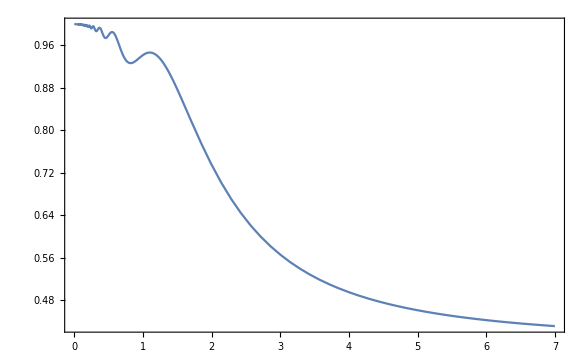

```mathematica
Plot[Fav/.A->2.2,{b1,0,7},Frame->True]
```

```mathematica
data=Cases[Plot[Fav/.A->2.2,{b1,0,7},Frame->True],Line[data_]:>data,-4,1][[1]];
```

```mathematica
Export["file1.dat",data,"Table"]
```

file1.dat

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["file.dat"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["file.txt"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["file.txt"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["file.txt"]]]
```